### Shadow Vector Field Construction for small h

#### Symbolic Code

```mathematica
Clear["Global`*"]; 
Remove["Global`*"];
(*Helper Functions *)
dot[f_,y_,k_] := Module[{i,fdot},
fdot = D[f,y]*f;
For[i = 2,i <= k,i++,
fdot = D[fdot,y]*f];
fdot]
computeYTilde[fi_,y_,h_,n_] := Module[{i,yTilde},
yTilde = y + h*fi;
i = 2;
While[i <= n,yTilde = yTilde + h^i/i! * dot[fi,y,i-1];i++];
yTilde
]

computeShadowVF[fOriginal_,ϕ_,h_,y_,n_,k_] := Module[{ fShadow = Table[Subscript[fShadow, i],{i,1,k}],deltaf = Table[Subscript[deltaf, i],{i,1,k}],yTilde,i},
     Subscript[fShadow, 1] = fOriginal; Subscript[deltaf, 1] = fOriginal;
For[i = 1,i < k,i++, (*k = no of terms in shadow vf *)
yTilde = computeYTilde[Subscript[fShadow, i],y,h,n]; (* n = No of terms in expansion *)
Subscript[deltaf, i+1] = D[ϕ - yTilde,{h,i+1}]/(i+1)!;
Subscript[fShadow, i+1]= Subscript[fShadow, i]+ h^(i)*Subscript[deltaf, i+1] 
];
Subscript[fShadow, k]]
```

```mathematica
(*Symbolic Testing and usage of above function *)
f = y^2 ;
ϕ = y + h*f;n = 2;k = 3;
fShadow = computeShadowVF[f,ϕ,h,y,n,k];
Simplify[fShadow/.{h->0.01}]
```

y^2 (1.-0.01 y+0.00025 y^2-6.×10^-6 y^3)

#### Test Numerically

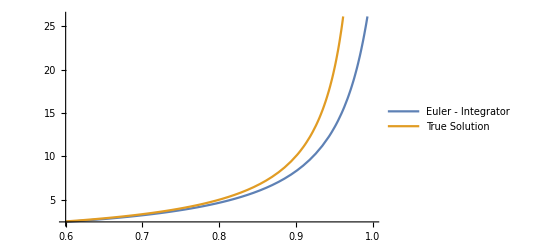
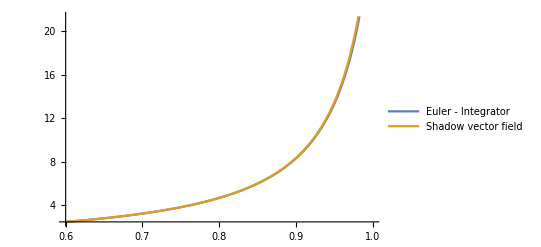
-Graphics-h = 0.01 | -Graphics-h = 0.01

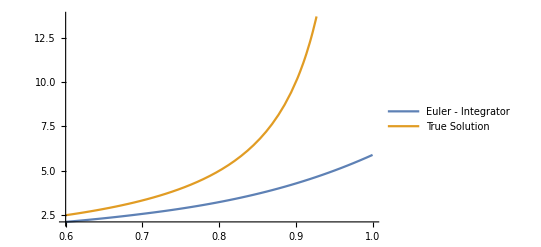
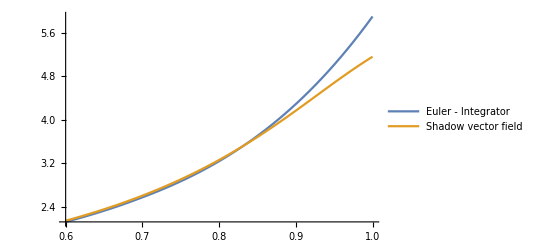
-Graphics-h = 0.1 | -Graphics-h = 0.1

```mathematica
(* Plot True output and integrated output together*)
Clear["Global`*"]; 
Remove["Global`*"];
(*Helper Functions *)
dot[f_,y_,k_] := Module[{i,fdot},
fdot = D[f,y]*f;
For[i = 2,i <= k,i++,
fdot = D[fdot,y]*f];
fdot]
computeYTilde[fi_,y_,h_,n_] := Module[{i,yTilde},
yTilde = y + h*fi;
i = 2;
While[i <= n,yTilde = yTilde + h^i/i! * dot[fi,y,i-1];i++];
yTilde
]

computeShadowVF[fOriginal_,ϕ_,h_,y_,n_,k_] := Module[{ fShadow = Table[Subscript[fShadow, i],{i,1,k}],deltaf = Table[Subscript[deltaf, i],{i,1,k}],yTilde,i},
     Subscript[fShadow, 1] = fOriginal; Subscript[deltaf, 1] = fOriginal;
For[i = 1,i < k,i++, (*k = no of terms in shadow vf *)
yTilde = computeYTilde[Subscript[fShadow, i],y,h,n]; (* n = No of terms in expansion *)
Subscript[deltaf, i+1] = D[ϕ - yTilde,{h,i+1}]/(i+1)!;
Subscript[fShadow, i+1]= Subscript[fShadow, i]+ h^(i)*Subscript[deltaf, i+1] 
];
Subscript[fShadow, k]]

hDiscrete = 0.01;
tFinal = 1;tInitial = 0.6;
nSteps = IntegerPart[tFinal / hDiscrete];
xSol = RecurrenceTable[{a[n+1]==a[n] + hDiscrete*a[n]^2,a[1]==1},a,{n,1,nSteps}];
fEuler = Interpolation[xSol];
p1 = Labeled[Plot[{fEuler[1 + nSteps*t],1/(1-t)},{t,tInitial,tFinal},PlotLegends->{"Euler - Integrator","True Solution"}],"h = 0.01"];
f = y^2;
ϕ = y + h*f;n = 2;k = 3;
fShadow = computeShadowVF[f,ϕ,h,y,n,k];
fplot[t_] := fShadow/.{y->y[t],h-> hDiscrete};
ySol = NDSolveValue[{y'[t] == fplot[t],y[0] == 1},y,{t,0,1},Method->{"DiscontinuityProcessing"->None}];
p2 = Labeled[Plot[{fEuler[1 + nSteps*t],ySol[t]},{t,tInitial,tFinal},PlotLegends->{"Euler - Integrator","Shadow vector field"}],"h = 0.01"];
Grid[{{p1,p2}}]

Clear["Global`*"]; 
Remove["Global`*"];
(*Helper Functions *)
dot[f_,y_,k_] := Module[{i,fdot},
fdot = D[f,y]*f;
For[i = 2,i <= k,i++,
fdot = D[fdot,y]*f];
fdot]
computeYTilde[fi_,y_,h_,n_] := Module[{i,yTilde},
yTilde = y + h*fi;
i = 2;
While[i <= n,yTilde = yTilde + h^i/i! * dot[fi,y,i-1];i++];
yTilde
]

computeShadowVF[fOriginal_,ϕ_,h_,y_,n_,k_] := Module[{ fShadow = Table[Subscript[fShadow, i],{i,1,k}],deltaf = Table[Subscript[deltaf, i],{i,1,k}],yTilde,i},
     Subscript[fShadow, 1] = fOriginal; Subscript[deltaf, 1] = fOriginal;
For[i = 1,i < k,i++, (*k = no of terms in shadow vf *)
yTilde = computeYTilde[Subscript[fShadow, i],y,h,n]; (* n = No of terms in expansion *)
Subscript[deltaf, i+1] = D[ϕ - yTilde,{h,i+1}]/(i+1)!;
Subscript[fShadow, i+1]= Subscript[fShadow, i]+ h^(i)*Subscript[deltaf, i+1] 
];
Subscript[fShadow, k]]

hDiscrete = 0.1;
tFinal = 1;tInitial = 0.6;
nSteps = IntegerPart[tFinal / hDiscrete];
xSol = RecurrenceTable[{a[n+1]==a[n] + hDiscrete*a[n]^2,a[1]==1},a,{n,1,nSteps}];
fEuler = Interpolation[xSol];
p1 = Labeled[Plot[{fEuler[1 + nSteps*t],1/(1-t)},{t,tInitial,tFinal},PlotLegends->{"Euler - Integrator","True Solution"}],"h = 0.1"];
f = y^2;
ϕ = y + h*f;n = 2;k = 3;
fShadow = computeShadowVF[f,ϕ,h,y,n,k];
fplot[t_] := fShadow/.{y->y[t],h-> hDiscrete};
ySol = NDSolveValue[{y'[t] == fplot[t],y[0] == 1},y,{t,0,1},Method->{"DiscontinuityProcessing"->None}];
p2 = Labeled[Plot[{fEuler[1 + nSteps*t],ySol[t]},{t,tInitial,tFinal},PlotLegends->{"Euler - Integrator","Shadow vector field"}],"h = 0.1"];
Grid[{{p1,p2}}]
```

#### Recursive Function for not small h ( h = 0.1)

```mathematica
(* Apply the above functions recursively*)
Clear["Global`*"]; 
Remove["Global`*"];
dot[f_,y_,k_] := Module[{i,fdot},
fdot = D[f,y]*f;
For[i = 2,i <= k,i++,
fdot = D[fdot,y]*f];
fdot]
computeYTilde[fi_,y_,h_,n_] := Module[{i,yTilde},
yTilde = y + h*fi;
i = 2;
While[i <= n,yTilde = yTilde + h^i/i! * dot[fi,y,i-1];i++];
yTilde
]

computeShadowVF[fOriginal_,ϕ_,h_,y_,n_,k_] := Module[{ fShadow = Table[Subscript[fShadow, i],{i,1,k}],deltaf = Table[Subscript[deltaf, i],{i,1,k}],yTilde,i},
     Subscript[fShadow, 1] = fOriginal; Subscript[deltaf, 1] = fOriginal;
For[i = 1,i < k,i++, (*k = no of terms in shadow vf *)
yTilde = computeYTilde[Subscript[fShadow, i],y,h,n]; (* n = No of terms in expansion *)
Subscript[deltaf, i+1] = D[ϕ - yTilde,{h,i+1}]/(i+1)!;
Subscript[fShadow, i+1]= Subscript[fShadow, i]+ h^(i)*Subscript[deltaf, i+1] 
];
Subscript[fShadow, k]]
fCleanUp[f_,y_,order_] := Module[{},
fClean = f/.{y->0};i = 1;
While[i <= order,
fClean = fClean + (D[f,{y,i}]/.{y->0})*1/i!*y^i; (* Coeff of y^i *)
i++];
fClean]
```

```mathematica
(*Only consider terms upto y^10 *)
f = y^2;
ϕ = y + h*f;n = 2;k = 3;
fNew = f;hStep = 0;deltah = 0.001;hFinal = 0.1;
While[hStep <= hFinal,
fNew = computeShadowVF[fNew,ϕ/.{h-> (hStep + δh)},δh,y,n,k];
fNew = fNew/.{δh -> deltah};
fNew = fCleanUp[fNew,y,10];
hStep = hStep + deltah]
```

```mathematica
fNew
```

0.+1. y^2-0.101 y^3+0.0128775 y^4-0.00184891 y^5+0.000285504 y^6-0.0000463226 y^7+7.7907×10^-6 y^8-1.3466×10^-6 y^9+2.37829×10^-7 y^10

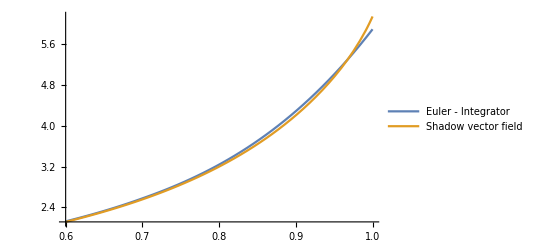
-Graphics-h = 0.1 | -Graphics-h = 0.1

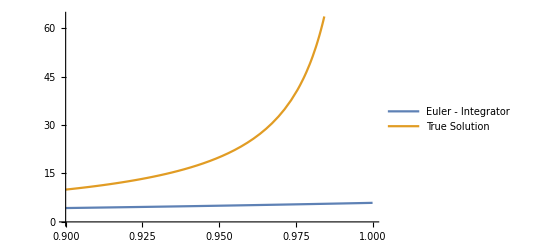
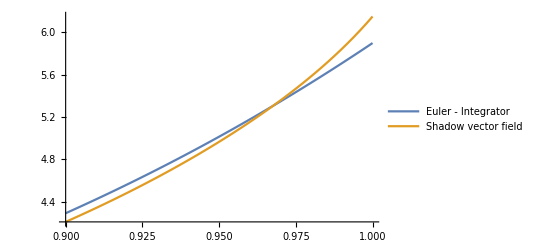
-Graphics-h = 0.1 | -Graphics-h = 0.1

```mathematica
hDiscrete = 0.1;
tFinal = 1;tInitial = 0.6;
nSteps = IntegerPart[tFinal / hDiscrete];
xSol = RecurrenceTable[{a[n+1]==a[n] + hDiscrete*a[n]^2,a[1]==1},a,{n,1,nSteps}];
fEuler = Interpolation[xSol];
p1 = Labeled[Plot[{fEuler[1 + nSteps*t],1/(1-t)},{t,tInitial,tFinal},PlotLegends->{"Euler - Integrator","True Solution"}],"h = 0.1"];

fNew = 0.+1. y^2-0.10100000000000005 y^3+0.012877499999999986 y^4-0.001848905999999999 y^5+0.00028550427500000016 y^6-0.00004632256172500001 y^7+7.790698251123754*^-6 y^8-1.3466010149608202*^-6 y^9+2.3782936655733824*^-7 y^10; (* Specific to step size of h = 0.1 *)

fplot[t_] := fNew/.{y->y[t]};
ySol = NDSolveValue[{y'[t] == fplot[t],y[0] == 1},y,{t,0,1},Method->{"DiscontinuityProcessing"->None}];
p2 = Labeled[Plot[{fEuler[1 + nSteps*t],ySol[t]},{t,tInitial,tFinal},PlotLegends->{"Euler - Integrator","Shadow vector field"}],"h = 0.1"];
Grid[{{p1,p2}}]
tInitial = 0.9;
p1 = Labeled[Plot[{fEuler[1 + nSteps*t],1/(1-t)},{t,tInitial,tFinal},PlotLegends->{"Euler - Integrator","True Solution"}],"h = 0.1"];
p2 = Labeled[Plot[{fEuler[1 + nSteps*t],ySol[t]},{t,tInitial,tFinal},PlotLegends->{"Euler - Integrator","Shadow vector field"}],"h = 0.1"];
Grid[{{p1,p2}}]
```